(4 BesselJ[1,π u]^2)/(π^2 u^2)

(4 (BesselJ[1,π u]/(π u)-BesselJ[1,π rat u]/(π u))^2)/(1-rat)^2

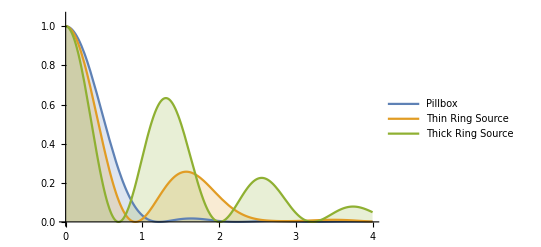

```mathematica
Remove["Global`*"]
a=1;
with[u_]=BesselJ[1,π u]/(π u);
with[u_]=(with[u]/Limit[with[υ],υ->0])^2//Simplify

without[u_]=(BesselJ[1,π u]/( π u ))-(BesselJ[1,rat π u]/(π u));
without[u_]=(without[u]/Limit[without[υ],υ->0])^2

Plot[{Abs[with[u]],without[u]/.rat->.3,without[u]/.rat->.7},{u,0,4},PlotStyle->Thick,Filling->Axis,FillingStyle->Automatic,PlotStyle->"Visibility with and without a central source",PlotRange->{Automatic,{0,1.05}},PlotLegends->{"Pillbox","Thin Ring Source","Thick Ring Source"}]
```